# Dipole v2, |J|^2 at large kT

## Convention on vectors

```mathematica
GNr[{x1_,x2_}]:=Sqrt[x1^2+x2^2];
GNang[{x1_,x2_}]:=ArcTan[x1,x2];
GNtoPolar[{x_,y_}]:={GNr[{x,y}],GNang[{x,y}]};
GNtoCartesian[{r_,θ_}]:={r Cos[θ],r Sin[θ]};
```

```mathematica
GNr[{1,2}]
```

√5

```mathematica
Clear[GNcdotinC,GNcdotinP];
GNcdotinC[{x1_,x2_},{k1_,k2_}]:={x1,x2}.{k1,k2};
GNcdotinP[{x_,θx_},{k_,θk_}]:=x k Cos[θx-θk];
GNcdotinC[{x1_,x2_}]:=x1^2+x2^2;
GNcdotinP[{x_,θx_}]:=x^2
```

```mathematica
x1=1;
x2=2;
x3=1.2;
x4=5;
GNcdotinC[{x1,x2},{x3,x4}]
GNcdotinC[{x1,x2}]
xinP=GNtoPolar[{x1,x2}];
yinP=GNtoPolar[{x3,x4}];
GNcdotinP[xinP,yinP]
GNcdotinP[xinP]
```

11.2

5

11.2

5

## Single to relative coordinates

```mathematica
FNReltoSingle[{bx_,by_},{rA_,rAθ_},{rB_,rBθ_}]:=Module[{x1u,x2u,x3u,x4u},
x1u={rA/2 Cos[rAθ],rA/2 Sin[rAθ]};
x2u={-rA/2 Cos[rAθ],-rA/2 Sin[rAθ]};
x3u={bx+rB/2 Cos[rBθ],by+rB/2 Sin[rBθ]};
x4u={bx-rB/2 Cos[rBθ],by-rB/2 Sin[rBθ]};
{x1u,x2u,x3u,x4u}
];
```

```mathematica
bx=0;
by=3(*2*);
rA=2;
rAθ=0;
rB=2;
rBθ=π/3;
{x1u,x2u,x3u,x4u}=FNReltoSingle[{bx,by},{rA,rAθ},{rB,rBθ}];
x1u//Print;
x2u//Print;
x3u//Print;
x4u//Print;
```

{1,0}

{-1,0}

{1/2,3+(√3)/2}

{-1/2,3-(√3)/2}

## Plot dipole config

```mathematica
Clear[FNPlotDipole];
FNPlotDipole[x1u_,x2u_,x3u_,x4u_]:=
Module[{bu},
bu=(x3u+x4u)/2-(x1u+x2u)/2;
res=
Show[
(*Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],*)Graphics[{Black,Thick,Line[{x1u,x2u}]}],Graphics[{Blue,Disk[x1u,.1]}],Graphics[{Red,Disk[x2u,.1]}],
Graphics[{Black,Thick,Line[{x3u,x4u}]}],Graphics[{Blue,Thick,Circle[x3u,.1]}],Graphics[{Red,Thick,Circle[x4u,.1]}],
Graphics[{Black,Thick,Dashed,Line[{{0,0},bu}]}],
(*Axes->True,*)
LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Clear[FNPlotDipoleRel];
FNPlotDipoleRel[{bx_,by_},{rA_,rAθ_},{rB_,rBθ_}]:=Module[{x1u,x2u,x3u,x4u},
{x1u,x2u,x3u,x4u}=FNReltoSingle[{bx,by},{rA,rAθ},{rB,rBθ}];
FNPlotDipole[x1u,x2u,x3u,x4u]
];
```

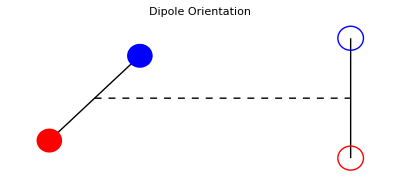

-Graphics-

```mathematica
bx=2;
by=0(*2*);
rA=1;
rAθ=π/4;
rB=1;
rBθ=π/2;
{x1u,x2u,x3u,x4u}=FNReltoSingle[{bx,by},{rA,rAθ},{rB,rBθ}];
FNPlotDipoleRel[{bx,by},{rA,rAθ},{rB,rBθ}]
FNPlotDipole[x1u,x2u,x3u,x4u]
```

## |J|^2

```mathematica
Clear[FNJ2LargekT];
FNJ2LargekT=
Compile[
{{k0,_Real},{ϕ,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{
kinC,
x1inC,x2inC,x3inC,x4inC,xsinC,TNxmninC,
x12,x13,x14,x23,x24,x34,
θ12,θ13,θ14,θ23,θ24,θ34,
Q1inC,Q2inC,Q3inC,Q4inC,QsinC,
Q1,Q2,Q3,Q4,Qs,
θQ1,θQ2,θQ3,θQ4,θQs,
B1,
FNfmn,FNgmn,FNhmn,
TNcmn,
resp1,resp2,resp3
},

kinC=GNtoCartesian[{k0,ϕ}];

x1inC={x1x,x1y};
x2inC={x2x,x2y};
x3inC={x3x,x3y};
x4inC={x4x,x4y};
xsinC={x1inC,x2inC,x3inC,x4inC};
TNxmninC=Table[xsinC[[m]]-xsinC[[n]],{m,1,4},{n,1,4}];

{x12,θ12}=GNtoPolar[TNxmninC[[1,2]]];
{x13,θ13}=GNtoPolar[TNxmninC[[1,3]]];
{x14,θ14}=GNtoPolar[TNxmninC[[1,4]]];
{x23,θ23}=GNtoPolar[TNxmninC[[2,3]]];
{x24,θ24}=GNtoPolar[TNxmninC[[2,4]]];
{x34,θ34}=GNtoPolar[TNxmninC[[3,4]]];


Q1inC=-TNxmninC[[1,3]]/x13^2+TNxmninC[[1,4]]/x14^2;
Q2inC=TNxmninC[[2,3]]/x23^2-TNxmninC[[2,4]]/x24^2;
Q3inC=-TNxmninC[[1,3]]/x13^2+TNxmninC[[2,3]]/x23^2;
Q4inC=TNxmninC[[1,4]]/x14^2-TNxmninC[[2,4]]/x24^2;
QsinC={Q1inC,Q2inC,Q3inC,Q4inC};


{Q1,θQ1}=GNtoPolar[Q1inC];
{Q2,θQ2}=GNtoPolar[Q2inC];
{Q3,θQ3}=GNtoPolar[Q3inC];
{Q4,θQ4}=GNtoPolar[Q4inC];
Qs={Q1,Q2,Q3,Q4};
θQs={θQ1,θQ2,θQ3,θQ4};

B1=1/(4 π^2)Sum[GNcdotinC[q],{q,Qs}];

(*FNfmn[m_,n_]:=1/(4 π^2)GNcdotinC[QsinC[[m]],QsinC[[n]]];*)
(*FNgmn[m_,n_]:=-1/(2 π^2)Qs[[m]]Qs[[n]]Cos[θQs[[m]]+θQs[[n]]];*)
(*FNhmn[m_,n_]:=-1/(2 π^2)Qs[[m]]Qs[[n]]Sin[θQs[[m]]+θQs[[n]]];*)



TNcmn=Table[Cos[GNcdotinC[kinC,(xsinC[[m]]-xsinC[[n]])]],{m,1,4},{n,1,4}];

resp1=1/(4 π^2)Sum[
qm=QsinC[[m]];qn=QsinC[[n]];GNcdotinC[qm,qn]TNcmn[[m,n]],{m,1,4},{n,1,4}];

resp2=-1/(2 π^2)Sum[
(Cos[θQs[[m]]+θQs[[n]]-2ϕ])Qs[[m]]Qs[[n]]TNcmn[[m,n]],{m,3,4},{n,1,2}];

1/k0^4*(resp1+resp2)

],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
]
```

CompiledFunction[…]

```mathematica
Clear[FNJ2LargekTxy];
FNJ2LargekTxy[{kx_,ky_},{x1x_,x1y_},{x2x_,x2y_},{x3x_,x3y_},{x4x_,x4y_}]:=Module[{k,ϕ},
{k,ϕ}=GNtoPolar[{kx,ky}];
FNJ2LargekT[k,ϕ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]];

Clear[FNJ2LargekTRel];
FNJ2LargekTRel[{kx_,ky_},{bx_,by_},{rA_,rAθ_},{rB_,rBθ_}]:=Module[{k,ϕ,x1u,x2u,x3u,x4u},
{k,ϕ}=GNtoPolar[{kx,ky}];
{x1u,x2u,x3u,x4u}=FNReltoSingle[{bx,by},{rA,rAθ},{rB,rBθ}];
FNJ2LargekTxy[{kx,ky},x1u,x2u,x3u,x4u]];
```

### test

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=2;
by=0(*2*);
rA=1;
rAθ=π/4;
rB=1;
rBθ=π/2;
FNPlotDipoleRel[{bx,by},{rA,rAθ},{rB,rBθ}]//Print;
```

-Graphics-

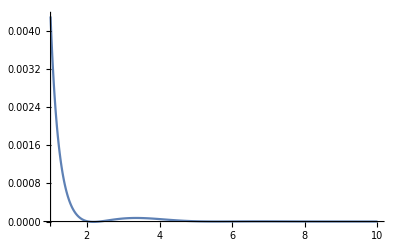

```mathematica
Plot[FNJ2LargekTRel[{k,0},{bx,by},{rA,rAθ},{rB,rBθ}],{k,1,10},PlotRange->All]
```

```mathematica
matrix2D=Table[FNJ2LargekTRel[{kx,ky},{bx,by},{rA,rAθ},{rB,rBθ}],{kx,-10,10,.1},{ky,-10,10,.1}];
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

Power::infy: Infinite expression 1/0. encountered.

```mathematica
MatrixPlot[matrix2D,PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
ListContourPlot[matrix2D,PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## v^2

```mathematica
Clear[FNv2LargekT];
FNv2LargekT=
Compile[
{{k0,_Real},{ϕ,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{
kinC,
x1inC,x2inC,x3inC,x4inC,xsinC,TNxmninC,
x12,x13,x14,x23,x24,x34,
θ12,θ13,θ14,θ23,θ24,θ34,
Q1inC,Q2inC,Q3inC,Q4inC,QsinC,
Q1,Q2,Q3,Q4,Qs,
θQ1,θQ2,θQ3,θQ4,θQs,
B1,
FNfmn,FNgmn,FNhmn,
TNcmn,
resp1,resp2,resp3
},

kinC=GNtoCartesian[{k0,ϕ}];

x1inC={x1x,x1y};
x2inC={x2x,x2y};
x3inC={x3x,x3y};
x4inC={x4x,x4y};
xsinC={x1inC,x2inC,x3inC,x4inC};
TNxmninC=Table[xsinC[[m]]-xsinC[[n]],{m,1,4},{n,1,4}];

{x12,θ12}=GNtoPolar[TNxmninC[[1,2]]];
{x13,θ13}=GNtoPolar[TNxmninC[[1,3]]];
{x14,θ14}=GNtoPolar[TNxmninC[[1,4]]];
{x23,θ23}=GNtoPolar[TNxmninC[[2,3]]];
{x24,θ24}=GNtoPolar[TNxmninC[[2,4]]];
{x34,θ34}=GNtoPolar[TNxmninC[[3,4]]];


Q1inC=-TNxmninC[[1,3]]/x13^2+TNxmninC[[1,4]]/x14^2;
Q2inC=TNxmninC[[2,3]]/x23^2-TNxmninC[[2,4]]/x24^2;
Q3inC=-TNxmninC[[1,3]]/x13^2+TNxmninC[[2,3]]/x23^2;
Q4inC=TNxmninC[[1,4]]/x14^2-TNxmninC[[2,4]]/x24^2;
QsinC={Q1inC,Q2inC,Q3inC,Q4inC};


{Q1,θQ1}=GNtoPolar[Q1inC];
{Q2,θQ2}=GNtoPolar[Q2inC];
{Q3,θQ3}=GNtoPolar[Q3inC];
{Q4,θQ4}=GNtoPolar[Q4inC];
Qs={Q1,Q2,Q3,Q4};
θQs={θQ1,θQ2,θQ3,θQ4};

B1=1/(4 π^2)Sum[GNcdotinC[q],{q,Qs}];

(*FNfmn[m_,n_]:=1/(4 π^2)GNcdotinC[QsinC[[m]],QsinC[[n]]];*)
(*FNgmn[m_,n_]:=-1/(2 π^2)Qs[[m]]Qs[[n]]Cos[θQs[[m]]+θQs[[n]]];*)
(*FNhmn[m_,n_]:=-1/(2 π^2)Qs[[m]]Qs[[n]]Sin[θQs[[m]]+θQs[[n]]];*)



TNcmn=Table[Cos[GNcdotinC[kinC,(xsinC[[m]]-xsinC[[n]])]],{m,1,4},{n,1,4}];

resp1=1/(4 π^2)Sum[
qm=QsinC[[m]];qn=QsinC[[n]];GNcdotinC[qm,qn]TNcmn[[m,n]],{m,1,4},{n,1,4}];

resp2=-1/(2 π^2)Sum[
(Cos[θQs[[m]]+θQs[[n]]-2ϕ])Qs[[m]]Qs[[n]]TNcmn[[m,n]],{m,3,4},{n,1,2}];

1/k0^4*(resp1+resp2)

],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
]
```

CompiledFunction[…]

```mathematica
Clear[FNJ2LargekTxy];
FNJ2LargekTxy[{kx_,ky_},{x1x_,x1y_},{x2x_,x2y_},{x3x_,x3y_},{x4x_,x4y_}]:=Module[{k,ϕ},
{k,ϕ}=GNtoPolar[{kx,ky}];
FNJ2LargekT[k,ϕ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]];

Clear[FNJ2LargekTRel];
FNJ2LargekTRel[{kx_,ky_},{bx_,by_},{rA_,rAθ_},{rB_,rBθ_}]:=Module[{k,ϕ,x1u,x2u,x3u,x4u},
{k,ϕ}=GNtoPolar[{kx,ky}];
{x1u,x2u,x3u,x4u}=FNReltoSingle[{bx,by},{rA,rAθ},{rB,rBθ}];
FNJ2LargekTxy[{kx,ky},x1u,x2u,x3u,x4u]];
```

### test

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=2;
by=0(*2*);
rA=1;
rAθ=π/4;
rB=1;
rBθ=π/2;
FNPlotDipoleRel[{bx,by},{rA,rAθ},{rB,rBθ}]//Print;
```

-Graphics-

```mathematica
Plot[FNJ2LargekTRel[{k,0},{bx,by},{rA,rAθ},{rB,rBθ}],{k,1,10},PlotRange->All]
```

-Graphics-

```mathematica
matrix2D=Table[FNJ2LargekTRel[{kx,ky},{bx,by},{rA,rAθ},{rB,rBθ}],{kx,-10,10,.1},{ky,-10,10,.1}];
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

Power::infy: Infinite expression 1/0. encountered.

```mathematica
MatrixPlot[matrix2D,PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
ListContourPlot[matrix2D,PlotRange->All,PlotLegends->Automatic]
```

-Graphics-